# Program for Cases Management in Israel

## Curve of Totals

```mathematica
SetDirectory["/Users/zhuohuizhang/Dropbox/israelcases"]
```

/Users/zhuohuizhang/Dropbox/IsraelCases

```mathematica
WebpageContent=Import["israelhealth.htm","Text"];
```

```mathematica
"<tr class=\"zbTRBlue2 zebraPhone\" id=\"TRItem_603e8417-0f76-4b93-884e-f8288d8e6100_3029\"><td class=\"gvDate\" >11.03.2020</td><td class=\"GovXMainTitleContent\"><a href=\"https://www.health.gov.il/NewsAndEvents/SpokemanMesseges/Pages/11032020_13.aspx\" title=\"חולה מספר 78 - מאזור הדרום, בת 49, מגע הדוק של חולה מאומת\" class=\"pagesListLink\" target=\"_blank\"><span xmlns:GxMSSettings=\"urn:GxMSSettings\" xmlns:ddwrt=\"http://schemas.microsoft.com/WebParts/v2/DataView/runtime\">חולה מספר 78 - מאזור הדרום, בת 49, מגע הדוק של חולה מאומת</span><a></td></tr>"
```

<tr class="zbTRBlue2 zebraPhone" id="TRItem_603e8417-0f76-4b93-884e-f8288d8e6100_3029"><td class="gvDate" >11.03.2020</td><td class="GovXMainTitleContent"><a href="https://www.health.gov.il/NewsAndEvents/SpokemanMesseges/Pages/11032020_13.aspx" title="חולה מספר 78 - מאזור הדרום, בת 49, מגע הדוק של חולה מאומת" class="pagesListLink" target="_blank"><span xmlns:GxMSSettings="urn:GxMSSettings" xmlns:ddwrt="http://schemas.microsoft.com/WebParts/v2/DataView/runtime">חולה מספר 78 - מאזור הדרום, בת 49, מגע הדוק של חולה מאומת</span><a></td></tr>

```mathematica
hexstring={CharacterRange["0","9"],CharacterRange["a","f"]}..;
hebrewname=Except["<"]..;
purenumber=CharacterRange["0","9"]..;
```

```mathematica
PatternForDate="<td class=\"gvDate\" >"~~purenumber~~"."~~purenumber~~"."~~purenumber~~"</td>";
PatternForContent="<span xmlns:GxMSSettings=\"urn:GxMSSettings\" xmlns:ddwrt=\"http://schemas.microsoft.com/WebParts/v2/DataView/runtime\">"~~hebrewname~~"</span>";
```

```mathematica
ListOfNewsTitles={StringCases[#[[1]],purenumber~~"."~~purenumber~~"."~~purenumber][[1]],StringDelete[#[[2]],{"<span xmlns:GxMSSettings=\"urn:GxMSSettings\" xmlns:ddwrt=\"http://schemas.microsoft.com/WebParts/v2/DataView/runtime\">","</span>"}]}&/@Partition[StringCases[WebpageContent,{PatternForDate,PatternForContent}],2];
```

```mathematica
GetNumber[str_]:=StringCases[#,purenumber]&/@(Join[StringCases[str,{"מספר "~~purenumber~~"-"~~purenumber,"מס' "~~purenumber~~"-"~~purenumber,"חולה "~~purenumber~~"-"~~purenumber}],StringCases[str,{"מספר "~~purenumber,"מס' "~~purenumber,"חולה "~~purenumber}],StringCases[str,{"ו–"~~purenumber,","~~Whitespace~~purenumber}]])//Flatten//DeleteDuplicates;
CalendarPatients={#[[1]],GetNumber[#[[2]]]}&/@ListOfNewsTitles;
```

```mathematica
DateListCorona=DateString[#,{"Day",".","Month",".","Year"}]&/@DateRange[DateObject[{2020,2,28}],Today];
PatientListGross=Association[Table[date->(ToExpression/@( Select[CalendarPatients,#[[1]]==DateString[date,{"Day",".","Month",".","Year"}]&] ⟦All,2⟧//Flatten//DeleteDuplicates//Sort)),{date,DateRange[DateObject[{2020,2,28}],Today]}]];
PatientListRefined=Module[{historicalpatients,k,refinedlist},
historicalpatients={2,3,4,5};
refinedlist={};
For[k=DateObject[{2020,2,28},"Day","Gregorian",2.],k≤ Today,k=k+Quantity[1,"Days"],
refinedlist=Append[refinedlist,{k,Complement[PatientListGross[k],historicalpatients],Max[Union[historicalpatients,PatientListGross[k]]],Length[Complement[PatientListGross[k],historicalpatients]]}];
historicalpatients=Union[historicalpatients,PatientListGross[k]];
];
refinedlist
]
```

{{Day: Fri 28 Feb 2020,{6,7},7,2},{Day: Sat 29 Feb 2020,{},7,0},{Day: Sun 1 Mar 2020,{8,9,10},10,3},{Day: Mon 2 Mar 2020,{11,12},12,2},{Day: Tue 3 Mar 2020,{},12,0},{Day: Wed 4 Mar 2020,{13,14,15},15,3},{Day: Thu 5 Mar 2020,{16,17},17,2},{Day: Fri 6 Mar 2020,{19,20,21},21,3},{Day: Sat 7 Mar 2020,{18,22,23,24,25},25,5},{Day: Sun 8 Mar 2020,{26,27,28,29},29,4},{Day: Mon 9 Mar 2020,{30,31,32,33,34,35,36,37,39,40,42,43,44,45,46,47,48,49,50},50,19},{Day: Tue 10 Mar 2020,{51,52,53,56,57,58,59,60,61,62,63,65,66,67,70},70,15},{Day: Wed 11 Mar 2020,{64,71,72,73,74,75,76,77,78,79,80,81,82},82,13},{Day: Thu 12 Mar 2020,{83,84,87,89,91,92,93,94,95,96},96,10},{Day: Fri 13 Mar 2020,{97,99,100,101,102,103,104,105,106,107,108,109,110,111,113,114,115,116,118,119,122,123,125,126,127},127,25},{Day: Sat 14 Mar 2020,{129,133,134,135,137,138,140,141,146,147,148,149,150,151,153,155,158,163,165,166,167,170,171,172,175,177,178,179,180,195},195,30},{Day: Sun 15 Mar 2020,{},195,0}}

```mathematica
PatientListRefined={{DateObject[{2020,2,28},"Day","Gregorian",2.],{6,7},7,2},{DateObject[{2020,2,29},"Day","Gregorian",2.],{},7,0},{DateObject[{2020,3,1},"Day","Gregorian",2.],{8,9,10},10,3},{DateObject[{2020,3,2},"Day","Gregorian",2.],{11,12},12,2},{DateObject[{2020,3,3},"Day","Gregorian",2.],{},12,0},{DateObject[{2020,3,4},"Day","Gregorian",2.],{13,14,15},15,3},{DateObject[{2020,3,5},"Day","Gregorian",2.],{16,17},17,2},{DateObject[{2020,3,6},"Day","Gregorian",2.],{19,20,21},21,3},{DateObject[{2020,3,7},"Day","Gregorian",2.],{18,22,23,24,25},25,5},{DateObject[{2020,3,8},"Day","Gregorian",2.],{26,27,28,29},29,4},{DateObject[{2020,3,9},"Day","Gregorian",2.],{30,31,32,33,34,35,36,37,39,40,42,43,44,45,46,47,48,49,50},50,19},{DateObject[{2020,3,10},"Day","Gregorian",2.],{51,52,53,56,57,58,59,60,61,62,63,65,66,67,70},70,15},{DateObject[{2020,3,11},"Day","Gregorian",2.],{64,71,72,73,74,75,76,77,78,79,80,81,82},82,13},{DateObject[{2020,3,12},"Day","Gregorian",2.],{83,84,87,89,91,92,93,94,95,96},96,10},{DateObject[{2020,3,13},"Day","Gregorian",2.],{97,99,100,101,102,103,104,105,106,107,108,109,110,111,113,114,115,116,118,119,122,123,125,126,127},127,25},{DateObject[{2020,3,14},"Day","Gregorian",2.],{129,133,134,135,137,138,140,141,146,147,148,149,150,151,153,155,158,163,165,166,167,170,171,172,175,177,178,179,180,195},195,30}};
```

```mathematica
PatientListNumber=PatientListRefined⟦All,{1,3}⟧;
PatientListIncrement=PatientListRefined⟦All,{1,4}⟧;
```

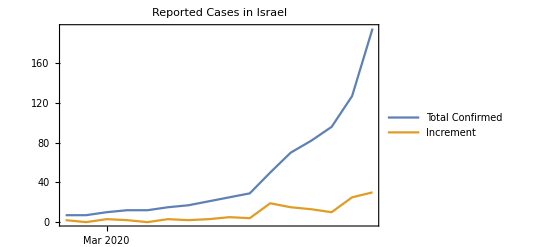

```mathematica
{PatientListNumber,PatientListIncrement}//DateListPlot[#,PlotLabel->"Reported Cases in Israel",PlotLegends->{"Total Confirmed","Increment"},PlotRange->All]&
```

```mathematica
Export["images/totalcases.svg",{PatientListNumber,PatientListIncrement}//DateListPlot[#,PlotLabel->"Reported Cases in Israel",PlotLegends->{"Total Confirmed","Increment"},PlotRange->All]&,"SVG"]
```

images/totalcases.svg

## The Program

## List of Geographical Data

### Countries

```mathematica
CountryList={Entity["Country","Afghanistan"],Entity["Country","AlandIslands"],Entity["Country","Albania"],Entity["Country","Algeria"],Entity["Country","AmericanSamoa"],Entity["Country","Andorra"],Entity["Country","Angola"],Entity["Country","Anguilla"],Entity["Country","AntiguaBarbuda"],Entity["Country","Argentina"],Entity["Country","Armenia"],Entity["Country","Aruba"],Entity["Country","Australia"],Entity["Country","Austria"],Entity["Country","Azerbaijan"],Entity["Country","Bahamas"],Entity["Country","Bahrain"],Entity["Country","Bangladesh"],Entity["Country","Barbados"],Entity["Country","Belarus"],Entity["Country","Belgium"],Entity["Country","Belize"],Entity["Country","Benin"],Entity["Country","Bermuda"],Entity["Country","Bhutan"],Entity["Country","Bolivia"],Entity["Country","BonaireSintEustatiusAndSaba"],Entity["Country","BosniaHerzegovina"],Entity["Country","Botswana"],Entity["Country","BouvetIsland"],Entity["Country","Brazil"],Entity["Country","BritishIndianOceanTerritory"],Entity["Country","BritishVirginIslands"],Entity["Country","Brunei"],Entity["Country","Bulgaria"],Entity["Country","BurkinaFaso"],Entity["Country","Burundi"],Entity["Country","Cambodia"],Entity["Country","Cameroon"],Entity["Country","Canada"],Entity["Country","CapeVerde"],Entity["Country","CaymanIslands"],Entity["Country","CentralAfricanRepublic"],Entity["Country","Chad"],Entity["Country","Chile"],Entity["Country","China"],Entity["Country","ChristmasIsland"],Entity["Country","CocosKeelingIslands"],Entity["Country","Colombia"],Entity["Country","Comoros"],Entity["Country","CookIslands"],Entity["Country","CostaRica"],Entity["Country","Croatia"],Entity["Country","Cuba"],Entity["Country","Curacao"],Entity["Country","Cyprus"],Entity["Country","CzechRepublic"],Entity["Country","DemocraticRepublicCongo"],Entity["Country","Denmark"],Entity["Country","Djibouti"],Entity["Country","Dominica"],Entity["Country","DominicanRepublic"],Entity["Country","EastTimor"],Entity["Country","Ecuador"],Entity["Country","Egypt"],Entity["Country","ElSalvador"],Entity["Country","EquatorialGuinea"],Entity["Country","Eritrea"],Entity["Country","Estonia"],Entity["Country","Ethiopia"],Entity["Country","FalklandIslands"],Entity["Country","FaroeIslands"],Entity["Country","Fiji"],Entity["Country","Finland"],Entity["Country","France"],Entity["Country","FrenchGuiana"],Entity["Country","FrenchPolynesia"],Entity["Country","FrenchSouthernAndAntarcticLands"],Entity["Country","Gabon"],Entity["Country","Gambia"],Entity["Country","GazaStrip"],Entity["Country","Georgia"],Entity["Country","Germany"],Entity["Country","Ghana"],Entity["Country","Gibraltar"],Entity["Country","Greece"],Entity["Country","Greenland"],Entity["Country","Grenada"],Entity["Country","Guadeloupe"],Entity["Country","Guam"],Entity["Country","Guatemala"],Entity["Country","Guernsey"],Entity["Country","Guinea"],Entity["Country","GuineaBissau"],Entity["Country","Guyana"],Entity["Country","Haiti"],Entity["Country","Honduras"],Entity["Country","HongKong"],Entity["Country","Hungary"],Entity["Country","Iceland"],Entity["Country","India"],Entity["Country","Indonesia"],Entity["Country","Iran"],Entity["Country","Iraq"],Entity["Country","Ireland"],Entity["Country","IsleOfMan"],Entity["Country","Israel"],Entity["Country","Italy"],Entity["Country","IvoryCoast"],Entity["Country","Jamaica"],Entity["Country","Japan"],Entity["Country","Jersey"],Entity["Country","Jordan"],Entity["Country","Kazakhstan"],Entity["Country","Kenya"],Entity["Country","Kiribati"],Entity["Country","Kosovo"],Entity["Country","Kuwait"],Entity["Country","Kyrgyzstan"],Entity["Country","Laos"],Entity["Country","Latvia"],Entity["Country","Lebanon"],Entity["Country","Lesotho"],Entity["Country","Liberia"],Entity["Country","Libya"],Entity["Country","Liechtenstein"],Entity["Country","Lithuania"],Entity["Country","Luxembourg"],Entity["Country","Macau"],Entity["Country","Macedonia"],Entity["Country","Madagascar"],Entity["Country","Malawi"],Entity["Country","Malaysia"],Entity["Country","Maldives"],Entity["Country","Mali"],Entity["Country","Malta"],Entity["Country","MarshallIslands"],Entity["Country","Martinique"],Entity["Country","Mauritania"],Entity["Country","Mauritius"],Entity["Country","Mayotte"],Entity["Country","Mexico"],Entity["Country","Micronesia"],Entity["Country","Moldova"],Entity["Country","Monaco"],Entity["Country","Mongolia"],Entity["Country","Montenegro"],Entity["Country","Montserrat"],Entity["Country","Morocco"],Entity["Country","Mozambique"],Entity["Country","Myanmar"],Entity["Country","Namibia"],Entity["Country","Nauru"],Entity["Country","Nepal"],Entity["Country","Netherlands"],Entity["Country","NewCaledonia"],Entity["Country","NewZealand"],Entity["Country","Nicaragua"],Entity["Country","Niger"],Entity["Country","Nigeria"],Entity["Country","Niue"],Entity["Country","NorfolkIsland"],Entity["Country","NorthernMarianaIslands"],Entity["Country","NorthKorea"],Entity["Country","Norway"],Entity["Country","Oman"],Entity["Country","Pakistan"],Entity["Country","Palau"],Entity["Country","Panama"],Entity["Country","PapuaNewGuinea"],Entity["Country","Paraguay"],Entity["Country","Peru"],Entity["Country","Philippines"],Entity["Country","PitcairnIslands"],Entity["Country","Poland"],Entity["Country","Portugal"],Entity["Country","PuertoRico"],Entity["Country","Qatar"],Entity["Country","RepublicCongo"],Entity["Country","Reunion"],Entity["Country","Romania"],Entity["Country","Russia"],Entity["Country","Rwanda"],Entity["Country","SaintBarthelemy"],Entity["Country","SaintHelena"],Entity["Country","SaintKittsNevis"],Entity["Country","SaintLucia"],Entity["Country","SaintMartin"],Entity["Country","SaintPierreMiquelon"],Entity["Country","SaintVincentGrenadines"],Entity["Country","Samoa"],Entity["Country","SanMarino"],Entity["Country","SaoTomePrincipe"],Entity["Country","SaudiArabia"],Entity["Country","Senegal"],Entity["Country","Serbia"],Entity["Country","Seychelles"],Entity["Country","SierraLeone"],Entity["Country","Singapore"],Entity["Country","SintMaarten"],Entity["Country","Slovakia"],Entity["Country","Slovenia"],Entity["Country","SolomonIslands"],Entity["Country","Somalia"],Entity["Country","SouthAfrica"],Entity["Country","SouthGeorgiaAndTheSouthSandwichIslands"],Entity["Country","SouthKorea"],Entity["Country","SouthSudan"],Entity["Country","Spain"],Entity["Country","SriLanka"],Entity["Country","Sudan"],Entity["Country","Suriname"],Entity["Country","Svalbard"],Entity["Country","Swaziland"],Entity["Country","Sweden"],Entity["Country","Switzerland"],Entity["Country","Syria"],Entity["Country","Taiwan"],Entity["Country","Tajikistan"],Entity["Country","Tanzania"],Entity["Country","Thailand"],Entity["Country","Togo"],Entity["Country","Tokelau"],Entity["Country","Tonga"],Entity["Country","TrinidadTobago"],Entity["Country","Tunisia"],Entity["Country","Turkey"],Entity["Country","Turkmenistan"],Entity["Country","TurksCaicosIslands"],Entity["Country","Tuvalu"],Entity["Country","Uganda"],Entity["Country","Ukraine"],Entity["Country","UnitedArabEmirates"],Entity["Country","UnitedKingdom"],Entity["Country","UnitedStates"],Entity["Country","UnitedStatesMinorOutlyingIslands"],Entity["Country","UnitedStatesVirginIslands"],Entity["Country","Uruguay"],Entity["Country","Uzbekistan"],Entity["Country","Vanuatu"],Entity["Country","VaticanCity"],Entity["Country","Venezuela"],Entity["Country","Vietnam"],Entity["Country","WallisFutuna"],Entity["Country","WestBank"],Entity["Country","WesternSahara"],Entity["Country","Yemen"],Entity["Country","Zambia"],Entity["Country","Zimbabwe"]};
```

#### List of Israel Municipalities

```mathematica
rawmuni=Import["IsraelMunicipalities.xlsx","XLSX"];
```

Import::nffil: File IsraelMunicipalities.xlsx not found during Import.

```mathematica
AmbiguousCharacters1={"\"","”"};
AmbiguousCharacters2={"'","'","׳","’"};
AmbiguousCharacters3={"-"};
```

```mathematica
CreateStringPolymorphism[rule_]:=Module[{allchar1,allchar2,allchar3},
allchar1=StringCases[rule⟦1⟧,AmbiguousCharacters1];
allchar2=StringCases[rule⟦1⟧,AmbiguousCharacters2];
allchar3=StringCases[rule⟦1⟧,AmbiguousCharacters3];]
```

```mathematica
IsraelMunicipalitiesHebToEngWolfram=Association[(#⟦1⟧->#⟦2⟧&/@Join[Select[rawmuni[[1]],#[[3]]==1&],Select[rawmuni[[2]],#[[3]]==1&],Select[rawmuni[[3]],#[[3]]==1&],Select[rawmuni[[4]],#[[3]]==1&]]⟦All,1;;2⟧)//DeleteDuplicates];
```

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦3⟧ is longer than depth of object.

Part::partd: Part specification 1⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::argm: Part called with 0 arguments; 1 or more arguments are expected.

General::stop: Further output of Part::argm will be suppressed during this calculation.

```mathematica
IsraelMunicipalitiesHebToEng=Association[(#⟦1⟧->#⟦2⟧&/@Join[rawmuni[[1]],rawmuni[[2]],rawmuni[[3]],rawmuni[[4]]]⟦All,1;;2⟧)//DeleteDuplicates];
```

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦2⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦3⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::pkspec1: The expression $Failed cannot be used as a part specification.

Part::take: Cannot take positions 1 through 2 in $Failed.

Part::pkspec1: The expression All⟦1⟧→All⟦2⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

```mathematica
IsraelMunicipalitiesHebrew=Keys[IsraelMunicipalitiesHebToEng];
```

Keys::invrl: The argument Association[DeleteDuplicates[(#1⟦1⟧→#1⟦2⟧&)/@Join[rawmuni⟦1⟧,rawmuni⟦2⟧,rawmuni⟦3⟧,rawmuni⟦4⟧]⟦All,1;;2⟧]] is not a valid Association or a list of rules.

## Specification of City Names

```mathematica
CityToWolframDataWestBank=Association[((#⟦2,1⟧->#)&/@{Entity["City",{"AbuDis","Jerusalem","WestBank"}],Entity["City",{"Abud","RamallahAndAlBireh","WestBank"}],Entity["City",{"Abwein","RamallahAndAlBireh","WestBank"}],Entity["City",{"AdDuhaysah","Bethlehem","WestBank"}],Entity["City",{"Ajjah","Jenin","WestBank"}],Entity["City",{"AlAmarri","RamallahAndAlBireh","WestBank"}],Entity["City",{"AlAraqah","Jenin","WestBank"}],Entity["City",{"AlArrub","Hebron","WestBank"}],Entity["City",{"AlAwja","Jericho","WestBank"}],Entity["City",{"AlAyzariyah","Jerusalem","WestBank"}],Entity["City",{"AlBirah","RamallahAndAlBireh","WestBank"}],Entity["City",{"AlFandaqumiyah","Jenin","WestBank"}],Entity["City",{"AlFarah","Tubas","WestBank"}],Entity["City",{"AlFawwar","Hebron","WestBank"}],Entity["City",{"AlfeMenashe","JudeaAndSamaria","Israel"}],Entity["City",{"AlHadr","Bethlehem","WestBank"}],Entity["City",{"AlJalazun","RamallahAndAlBireh","WestBank"}],Entity["City",{"AlJib","Jerusalem","WestBank"}],Entity["City",{"AlJiftlik","Jericho","WestBank"}],Entity["City",{"AlJudaydah","Jenin","WestBank"}],Entity["City",{"AlJudayrah","Jerusalem","WestBank"}],Entity["City",{"AlKarmil","Hebron","WestBank"}],Entity["City",{"AllonShevut","JudeaAndSamaria","Israel"}],Entity["City",{"AlLubbanAsSarqiyah","Nablus","WestBank"}],Entity["City",{"AlMazraahAsSarqiyah","RamallahAndAlBireh","WestBank"}],Entity["City",{"AlMugayyir","Jenin","WestBank"}],Entity["City",{"AlMugayyir","RamallahAndAlBireh","WestBank"}],Entity["City",{"AlQubaybah","Jerusalem","WestBank"}],Entity["City",{"AlUbaydiyah","Bethlehem","WestBank"}],Entity["City",{"AlYamun","Jenin","WestBank"}],Entity["City",{"AlZaitounah","RamallahAndAlBireh","WestBank"}],Entity["City",{"Anabta","Tulkarm","WestBank"}],Entity["City",{"Anata","Jerusalem","WestBank"}],Entity["City",{"Anin","Jenin","WestBank"}],Entity["City",{"Anzah","Jenin","WestBank"}],Entity["City",{"AqbahJabbar","Jericho","WestBank"}],Entity["City",{"Aqqaba","Tubas","WestBank"}],Entity["City",{"Aqraba","Nablus","WestBank"}],Entity["City",{"Ariel","JudeaAndSamaria","Israel"}],Entity["City",{"Ariha","Jericho","WestBank"}],Entity["City",{"Arrabah","Jenin","WestBank"}],Entity["City",{"ArRam","Jerusalem","WestBank"}],Entity["City",{"Arranah","Jenin","WestBank"}],Entity["City",{"ArRihiyah","Hebron","WestBank"}],Entity["City",{"ArTas","Bethlehem","WestBank"}],Entity["City",{"Arurah","RamallahAndAlBireh","WestBank"}],Entity["City",{"AsirahAlQibliyah","Nablus","WestBank"}],Entity["City",{"AsirahAsSamaliyah","Nablus","WestBank"}],Entity["City",{"Askar","Nablus","WestBank"}],Entity["City",{"AsSamu","Hebron","WestBank"}],Entity["City",{"AsSawiyah","Nablus","WestBank"}],Entity["City",{"AsSuyuh","Hebron","WestBank"}],Entity["City",{"ATarah","RamallahAndAlBireh","WestBank"}],Entity["City",{"ATTaybah","Jenin","WestBank"}],Entity["City",{"ATTaybah","RamallahAndAlBireh","WestBank"}],Entity["City",{"Attil","Tulkarm","WestBank"}],Entity["City",{"Awarta","Nablus","WestBank"}],Entity["City",{"Aydah","Bethlehem","WestBank"}],Entity["City",{"Aynabus","Nablus","WestBank"}],Entity["City",{"AynYabrud","RamallahAndAlBireh","WestBank"}],Entity["City",{"AzmuT","Nablus","WestBank"}],Entity["City",{"AzZababidah","Jenin","WestBank"}],Entity["City",{"AzZahiriyah","Hebron","WestBank"}],Entity["City",{"AzZawiyah","Salfit","WestBank"}],Entity["City",{"Azzun","Qalqilya","WestBank"}],Entity["City",{"BalataAlBalad","Nablus","WestBank"}],Entity["City",{"BalaTah","Nablus","WestBank"}],Entity["City",{"Bala","Tulkarm","WestBank"}],Entity["City",{"BaniNaim","Hebron","WestBank"}],Entity["City",{"BaqahAsSarqiyah","Tulkarm","WestBank"}],Entity["City",{"BarTaahAsSarqiyah","Jenin","WestBank"}],Entity["City",{"Battir","Bethlehem","WestBank"}],Entity["City",{"Bayta","Nablus","WestBank"}],Entity["City",{"BaytAwwa","Hebron","WestBank"}],Entity["City",{"BaytDajan","Nablus","WestBank"}],Entity["City",{"BaytFajjar","Bethlehem","WestBank"}],Entity["City",{"BaytFurik","Nablus","WestBank"}],Entity["City",{"BaytIba","Nablus","WestBank"}],Entity["City",{"Baytillu","RamallahAndAlBireh","WestBank"}],Entity["City",{"BaytImrin","Nablus","WestBank"}],Entity["City",{"BaytJala","Bethlehem","WestBank"}],Entity["City",{"BaytKahil","Hebron","WestBank"}],Entity["City",{"BaytLahm","Bethlehem","WestBank"}],Entity["City",{"BaytLid","Tulkarm","WestBank"}],Entity["City",{"BaytLiqya","RamallahAndAlBireh","WestBank"}],Entity["City",{"BaytSahur","Bethlehem","WestBank"}],Entity["City",{"BaytSira","RamallahAndAlBireh","WestBank"}],Entity["City",{"BaytSurik","Jerusalem","WestBank"}],Entity["City",{"BaytUla","Hebron","WestBank"}],Entity["City",{"BaytUmmar","Hebron","WestBank"}],Entity["City",{"Baytuniya","RamallahAndAlBireh","WestBank"}],Entity["City",{"BaytUrAtTahta","RamallahAndAlBireh","WestBank"}],Entity["City",{"BetarIllit","JudeaAndSamaria","Israel"}],Entity["City",{"BetArye","JudeaAndSamaria","Israel"}],Entity["City",{"BetEl","JudeaAndSamaria","Israel"}],Entity["City",{"Biddu","Jerusalem","WestBank"}],Entity["City",{"Biddya","Salfit","WestBank"}],Entity["City",{"BirNabala","Jerusalem","WestBank"}],Entity["City",{"Birqin","Jenin","WestBank"}],Entity["City",{"BirZayt","RamallahAndAlBireh","WestBank"}],Entity["City",{"Bitin","RamallahAndAlBireh","WestBank"}],Entity["City",{"Bizzariya","Nablus","WestBank"}],Entity["City",{"Bruqin","Salfit","WestBank"}],Entity["City",{"Burin","Nablus","WestBank"}],Entity["City",{"Burqah","Nablus","WestBank"}],Entity["City",{"Burqah","RamallahAndAlBireh","WestBank"}],Entity["City",{"DayrAbuDaif","Jenin","WestBank"}],Entity["City",{"DayrAbuMasal","RamallahAndAlBireh","WestBank"}],Entity["City",{"DayrAlGusun","Tulkarm","WestBank"}],Entity["City",{"DayrAlHaTab","Nablus","WestBank"}],Entity["City",{"DayrAmmar","RamallahAndAlBireh","WestBank"}],Entity["City",{"DayrAsSaraf","Nablus","WestBank"}],Entity["City",{"DayrAsSudan","RamallahAndAlBireh","WestBank"}],Entity["City",{"DayrBalluT","Salfit","WestBank"}],Entity["City",{"DayrDibwan","RamallahAndAlBireh","WestBank"}],Entity["City",{"DayrIstiya","Salfit","WestBank"}],Entity["City",{"DayrJarir","RamallahAndAlBireh","WestBank"}],Entity["City",{"DayrSamit","Hebron","WestBank"}],Entity["City",{"Dhinnabah","Tulkarm","WestBank"}],Entity["City",{"Duma","Nablus","WestBank"}],Entity["City",{"DuraAlQar","RamallahAndAlBireh","WestBank"}],Entity["City",{"Dura","Hebron","WestBank"}],Entity["City",{"Efrata","JudeaAndSamaria","Israel"}],Entity["City",{"EinQiniyye","JudeaAndSamaria","Israel"}],Entity["City",{"Eli","JudeaAndSamaria","Israel"}],Entity["City",{"Elqana","JudeaAndSamaria","Israel"}],Entity["City",{"Fahmah","Jenin","WestBank"}],Entity["City",{"Faqquah","Jenin","WestBank"}],Entity["City",{"Farun","Tulkarm","WestBank"}],Entity["City",{"GevaBinyamin",Missing["NotAvailable"],"Israel"}],Entity["City",{"GivatZeev","JudeaAndSamaria","Israel"}],Entity["City",{"Hablah","Qalqilya","WestBank"}],Entity["City",{"Hajjah","Qalqilya","WestBank"}],Entity["City",{"Halhul","Hebron","WestBank"}],Entity["City",{"HarAdar","JudeaAndSamaria","Israel"}],Entity["City",{"Haras","Hebron","WestBank"}],Entity["City",{"HarbataAlMisbah","RamallahAndAlBireh","WestBank"}],Entity["City",{"Haris","Salfit","WestBank"}],Entity["City",{"Hashmonaim",Missing["NotAvailable"],"Israel"}],Entity["City",{"Hebron","Hebron","WestBank"}],Entity["City",{"HirbatAbuFalah","RamallahAndAlBireh","WestBank"}],Entity["City",{"Hizma","Jerusalem","WestBank"}],Entity["City",{"Hursa","Hebron","WestBank"}],Entity["City",{"Husan","Bethlehem","WestBank"}],Entity["City",{"Huwwara","Nablus","WestBank"}],Entity["City",{"Idhna","Hebron","WestBank"}],Entity["City",{"Iktaba","Tulkarm","WestBank"}],Entity["City",{"Illar","Tulkarm","WestBank"}],Entity["City",{"Immanuel","JudeaAndSamaria","Israel"}],Entity["City",{"Immatin","Qalqilya","WestBank"}],Entity["City",{"Jaba","Jenin","WestBank"}],Entity["City",{"Jaba","Jerusalem","WestBank"}],Entity["City",{"Jalbun","Jenin","WestBank"}],Entity["City",{"Jammain","Nablus","WestBank"}],Entity["City",{"Janin","Jenin","WestBank"}],Entity["City",{"Jayyus","Qalqilya","WestBank"}],Entity["City",{"JinsafuT","Qalqilya","WestBank"}],Entity["City",{"Jit","Qalqilya","WestBank"}],Entity["City",{"KafrAdDik","Salfit","WestBank"}],Entity["City",{"KafrAlLabad","Tulkarm","WestBank"}],Entity["City",{"KafrAqab","Jerusalem","WestBank"}],Entity["City",{"KafrDan","Jenin","WestBank"}],Entity["City",{"KafrJammal","Tulkarm","WestBank"}],Entity["City",{"KafrMalik","RamallahAndAlBireh","WestBank"}],Entity["City",{"KafrNimah","RamallahAndAlBireh","WestBank"}],Entity["City",{"KafrQaddum","Qalqilya","WestBank"}],Entity["City",{"KafrQallil","Nablus","WestBank"}],Entity["City",{"KafrRai","Jenin","WestBank"}],Entity["City",{"KafrTult","Qalqilya","WestBank"}],Entity["City",{"Kawbar","RamallahAndAlBireh","WestBank"}],Entity["City",{"KefarAdummim","JudeaAndSamaria","Israel"}],Entity["City",{"KiflHaris","Salfit","WestBank"}],Entity["City",{"KokhavYaaqov","JudeaAndSamaria","Israel"}],Entity["City",{"Kufayrit","Jenin","WestBank"}],Entity["City",{"Lappid","Hamerkaz","Israel"}],Entity["City",{"MaaleAdummim","JudeaAndSamaria","Israel"}],Entity["City",{"MajdalBaniFadil","Nablus","WestBank"}],Entity["City",{"Mardah","Salfit","WestBank"}],Entity["City",{"Maytalun","Jenin","WestBank"}],Entity["City",{"MazariAnNubari","RamallahAndAlBireh","WestBank"}],Entity["City",{"Misliyah","Jenin","WestBank"}],Entity["City",{"ModiinIllit",Missing["NotAvailable"],"Israel"}],Entity["City",{"ModiinMakkabimReut","Hamerkaz","Israel"}],Entity["City",{"MuhayyamDayrAmmar","RamallahAndAlBireh","WestBank"}],Entity["City",{"MuhayyamJanin","Jenin","WestBank"}],Entity["City",{"MuhayyamQalandiya","Jerusalem","WestBank"}],Entity["City",{"MuhayyamTulkarm","Tulkarm","WestBank"}],Entity["City",{"Nablus","Nablus","WestBank"}],Entity["City",{"Nahhalin","Bethlehem","WestBank"}],Entity["City",{"NazlatIsa","Tulkarm","WestBank"}],Entity["City",{"Nilin","RamallahAndAlBireh","WestBank"}],Entity["City",{"Nuba","Hebron","WestBank"}],Entity["City",{"NurSams","Tulkarm","WestBank"}],Entity["City",{"Ofra","JudeaAndSamaria","Israel"}],Entity["City",{"Qabalan","Nablus","WestBank"}],Entity["City",{"QabaTiyah","Jenin","WestBank"}],Entity["City",{"Qaffin","Tulkarm","WestBank"}],Entity["City",{"Qalqilyah","Qalqilya","WestBank"}],Entity["City",{"QarawatBaniHassan","Salfit","WestBank"}],Entity["City",{"QarawatBaniZayd","RamallahAndAlBireh","WestBank"}],Entity["City",{"QarneShomeron","JudeaAndSamaria","Israel"}],Entity["City",{"Qaryut","Nablus","WestBank"}],Entity["City",{"QaTannah","Jerusalem","WestBank"}],Entity["City",{"Qedummim","JudeaAndSamaria","Israel"}],Entity["City",{"Qibya","RamallahAndAlBireh","WestBank"}],Entity["City",{"QiryatArba","JudeaAndSamaria","Israel"}],Entity["City",{"Qusrah","Nablus","WestBank"}],Entity["City",{"Raba","Jenin","WestBank"}],Entity["City",{"Rafat","Jerusalem","WestBank"}],Entity["City",{"Rafat","Salfit","WestBank"}],Entity["City",{"RamAllah","RamallahAndAlBireh","WestBank"}],Entity["City",{"Ramin","Tulkarm","WestBank"}],Entity["City",{"Rammun","RamallahAndAlBireh","WestBank"}],Entity["City",{"Rantis","RamallahAndAlBireh","WestBank"}],Entity["City",{"Rujayb","Nablus","WestBank"}],Entity["City",{"Rummanah","Jenin","WestBank"}],Entity["City",{"SabasTiyah","Nablus","WestBank"}],Entity["City",{"Saffa","RamallahAndAlBireh","WestBank"}],Entity["City",{"Sair","Hebron","WestBank"}],Entity["City",{"Salfit","Salfit","WestBank"}],Entity["City",{"Salim","Nablus","WestBank"}],Entity["City",{"Sanniriya","Qalqilya","WestBank"}],Entity["City",{"Sanur","Jenin","WestBank"}],Entity["City",{"Sarrah","Nablus","WestBank"}],Entity["City",{"SarTah","Salfit","WestBank"}],Entity["City",{"Sayda","Tulkarm","WestBank"}],Entity["City",{"ShaareTiqwa","JudeaAndSamaria","Israel"}],Entity["City",{"Shilo","JudeaAndSamaria","Israel"}],Entity["City",{"SilatAlHaritiyah","Jenin","WestBank"}],Entity["City",{"SilatAzZahr","Jenin","WestBank"}],Entity["City",{"Silwad","RamallahAndAlBireh","WestBank"}],Entity["City",{"Sinjil","RamallahAndAlBireh","WestBank"}],Entity["City",{"Siris","Jenin","WestBank"}],Entity["City",{"Suqba","RamallahAndAlBireh","WestBank"}],Entity["City",{"Surif","Hebron","WestBank"}],Entity["City",{"Taffuh","Hebron","WestBank"}],Entity["City",{"Talfit","Nablus","WestBank"}],Entity["City",{"TallAsSulTan","Rafah","GazaStrip"}],Entity["City",{"Tall","Nablus","WestBank"}],Entity["City",{"Talluzah","Nablus","WestBank"}],Entity["City",{"Talmon","JudeaAndSamaria","Israel"}],Entity["City",{"Tammun","Tubas","WestBank"}],Entity["City",{"Tarqumiya","Hebron","WestBank"}],Entity["City",{"Tayasir","Tubas","WestBank"}],Entity["City",{"Tubas","Tubas","WestBank"}],Entity["City",{"Tulkarm","Tulkarm","WestBank"}],Entity["City",{"Tuqu","Bethlehem","WestBank"}],Entity["City",{"Turmusayya","RamallahAndAlBireh","WestBank"}],Entity["City",{"Urif","Nablus","WestBank"}],Entity["City",{"Yabad","Jenin","WestBank"}],Entity["City",{"Yasid","Nablus","WestBank"}],Entity["City",{"Yatma","Nablus","WestBank"}],Entity["City",{"YaTTa","Hebron","WestBank"}],Entity["City",{"Zatarah","Bethlehem","WestBank"}],Entity["City",{"Zayta","Tulkarm","WestBank"}]})];
CityToWolframData=Association[Join[((#⟦2,1⟧->#)&/@Join[{Entity["City",{"AbuGhosh","Jerusalem","Israel"}],Entity["City",{"Adi","Northern","Israel"}],Entity["City",{"Afula","Northern","Israel"}],Entity["City",{"Akko","Northern","Israel"}],Entity["City",{"AlBurj","Hebron","WestBank"}],Entity["City",{"AlJalamah","Jenin","WestBank"}],Entity["City",{"AlJudayrah","Jerusalem","WestBank"}],Entity["City",{"Arad","Hadarom","Israel"}],Entity["City",{"AraraBaNegev","Hadarom","Israel"}],Entity["City",{"Arara","Haifa","Israel"}],Entity["City",{"Arrabe","Northern","Israel"}],Entity["City",{"Ashdod","Hadarom","Israel"}],Entity["City",{"Ashqelon","Hadarom","Israel"}],Entity["City",{"Atlit","Haifa","Israel"}],Entity["City",{"Aydah","Bethlehem","WestBank"}],Entity["City",{"Azur","TelAviv","Israel"}],Entity["City",{"BaqaJatt","Haifa","Israel"}],Entity["City",{"Basma","Haifa","Israel"}],Entity["City",{"BasmatTabun","Northern","Israel"}],Entity["City",{"BatHefer","Hamerkaz","Israel"}],Entity["City",{"BatYam","TelAviv","Israel"}],Entity["City",{"BeerSheva","Hadarom","Israel"}],Entity["City",{"BeerYaaqov","Hamerkaz","Israel"}],Entity["City",{"BeitJann","Northern","Israel"}],Entity["City",{"BeneAyish","Hadarom","Israel"}],Entity["City",{"BeneBeraq","Hamerkaz","Israel"}],Entity["City",{"BetDagan","Hamerkaz","Israel"}],Entity["City",{"BetShean","Northern","Israel"}],Entity["City",{"BetShemesh","Jerusalem","Israel"}],Entity["City",{"BetYizhaq","Hamerkaz","Israel"}],Entity["City",{"BinyaminaGivatAda","Haifa","Israel"}],Entity["City",{"BirElMaksur","Northern","Israel"}],Entity["City",{"BueineNujeidat","Northern","Israel"}],Entity["City",{"Buqata","Northern","Israel"}],Entity["City",{"Dabburiyya","Northern","Israel"}],Entity["City",{"DaliyatAlKarmelIsifya","Haifa","Israel"}],Entity["City",{"DeirHanna","Northern","Israel"}],Entity["City",{"Dimona","Hadarom","Israel"}],Entity["City",{"Eilabun","Northern","Israel"}],Entity["City",{"EinMahel","Northern","Israel"}],Entity["City",{"EinNaqquba","Jerusalem","Israel"}],Entity["City",{"Elad","Hamerkaz","Israel"}],Entity["City",{"Elat","Hadarom","Israel"}],Entity["City",{"Elyakhin","Hamerkaz","Israel"}],Entity["City",{"EvenYehuda","Hamerkaz","Israel"}],Entity["City",{"Fassuta","Northern","Israel"}],Entity["City",{"Fureidis","Hamerkaz","Israel"}],Entity["City",{"GanNer","Northern","Israel"}],Entity["City",{"GanneTiqwa","TelAviv","Israel"}],Entity["City",{"GanYavne","Hadarom","Israel"}],Entity["City",{"Gedera","Hamerkaz","Israel"}],Entity["City",{"GivatAvni","Northern","Israel"}],Entity["City",{"Givatayim","TelAviv","Israel"}],Entity["City",{"GivatEla","Northern","Israel"}],Entity["City",{"GivatShemuel","TelAviv","Israel"}],Entity["City",{"GlilYam","Hamerkaz","Israel"}],Entity["City",{"Hadera","Haifa","Israel"}],Entity["City",{"Haifa","Haifa","Israel"}],Entity["City",{"HazorHaGelilit","Northern","Israel"}],Entity["City",{"Herzeliyya","TelAviv","Israel"}],Entity["City",{"HodHaSharon","Hamerkaz","Israel"}],Entity["City",{"Holon","TelAviv","Israel"}],Entity["City",{"Hura","Hadarom","Israel"}],Entity["City",{"Hurfeish","Northern","Israel"}],Entity["City",{"Ibillin","Northern","Israel"}],Entity["City",{"Ibtin","Haifa","Israel"}],Entity["City",{"Iksal","Northern","Israel"}],Entity["City",{"Ilut","Northern","Israel"}],Entity["City",{"IrHahamisha","Northern","Israel"}],Entity["City",{"Jaffa","TelAviv","Israel"}],Entity["City",{"Jaljulye","Hamerkaz","Israel"}],Entity["City",{"Jerusalem","Jerusalem","Israel"}],Entity["City",{"Jish","Northern","Israel"}],Entity["City",{"JisrAzZarqa","Haifa","Israel"}],Entity["City",{"JudeideMaker","Northern","Israel"}],Entity["City",{"KaabiyyeTabbashHajaj","Northern","Israel"}],Entity["City",{"Kabul","Northern","Israel"}],Entity["City",{"KafarBara","Hamerkaz","Israel"}],Entity["City",{"KafarKama","Northern","Israel"}],Entity["City",{"KafarKanna","Northern","Israel"}],Entity["City",{"KafarManda","Northern","Israel"}],Entity["City",{"KafarMisr","Northern","Israel"}],Entity["City",{"KafarQara","Haifa","Israel"}],Entity["City",{"KafarQasem","Hamerkaz","Israel"}],Entity["City",{"KafarYasif","Northern","Israel"}],Entity["City",{"KaokabAbuAlHija","Northern","Israel"}],Entity["City",{"KarmeYosef","Hamerkaz","Israel"}],Entity["City",{"Karmiel","Northern","Israel"}],Entity["City",{"KefarHabad","Hamerkaz","Israel"}],Entity["City",{"KefarSava","Hamerkaz","Israel"}],Entity["City",{"KefarShemaryahu","TelAviv","Israel"}],Entity["City",{"KefarTavor","Northern","Israel"}],Entity["City",{"KefarWeradim","Northern","Israel"}],Entity["City",{"KefarYona","Hamerkaz","Israel"}],Entity["City",{"KisraSumei","Northern","Israel"}],Entity["City",{"KokhavYair","Hamerkaz","Israel"}],Entity["City",{"Kuseife","Hadarom","Israel"}],Entity["City",{"Lappid","Hamerkaz","Israel"}],Entity["City",{"Laqye","Hadarom","Israel"}],Entity["City",{"Lehavim","Hadarom","Israel"}],Entity["City",{"Lod","Hamerkaz","Israel"}],Entity["City",{"MaaleIron","Haifa","Israel"}],Entity["City",{"MaalotTarshiha","Northern","Israel"}],Entity["City",{"MajdalShams","Northern","Israel"}],Entity["City",{"Masade","Northern","Israel"}],Entity["City",{"Mashhed","Northern","Israel"}],Entity["City",{"Mattan","Hamerkaz","Israel"}],Entity["City",{"MazkeretBatya","Hamerkaz","Israel"}],Entity["City",{"Mazraa","Northern","Israel"}],Entity["City",{"MerkazShappira","Hadarom","Israel"}],Entity["City",{"Metar","Hadarom","Israel"}],Entity["City",{"MevasseratZiyyon","Jerusalem","Israel"}],Entity["City",{"Mielya","Northern","Israel"}],Entity["City",{"MigdalHaEmeq","Northern","Israel"}],Entity["City",{"MizpeRamon","Hadarom","Israel"}],Entity["City",{"ModiinMakkabimReut","Hamerkaz","Israel"}],Entity["City",{"Mugar","Northern","Israel"}],Entity["City",{"Muqeible","Northern","Israel"}],Entity["City",{"Nahariyya","Northern","Israel"}],Entity["City",{"Nahef","Northern","Israel"}],Entity["City",{"Naura","Northern","Israel"}],Entity["City",{"NazeratIllit","Northern","Israel"}],Entity["City",{"Nazerat","Northern","Israel"}],Entity["City",{"Nehalim","Hamerkaz","Israel"}],Entity["City",{"Nein","Northern","Israel"}],Entity["City",{"Nesher","Haifa","Israel"}],Entity["City",{"NesZiyyona","Hamerkaz","Israel"}],Entity["City",{"Netanya","Hamerkaz","Israel"}],Entity["City",{"Netivot","Hadarom","Israel"}],Entity["City",{"NofAyyalon","Hamerkaz","Israel"}],Entity["City",{"Nofit","Northern","Israel"}],Entity["City",{"Nordiyya","Hamerkaz","Israel"}],Entity["City",{"Ofaqim","Hadarom","Israel"}],Entity["City",{"Omer","Hadarom","Israel"}],Entity["City",{"Oranit","JudeaAndSamaria","Israel"}],Entity["City",{"OrAqiva","Haifa","Israel"}],Entity["City",{"OrYehuda","TelAviv","Israel"}],Entity["City",{"PardesHannaKarkur","Haifa","Israel"}],Entity["City",{"Pardesiyya","Hamerkaz","Israel"}],Entity["City",{"Peqiin","Northern","Israel"}],Entity["City",{"PetahTiqwa","Hamerkaz","Israel"}],Entity["City",{"Qalansawe","Hamerkaz","Israel"}],Entity["City",{"QaTannah","Jerusalem","WestBank"}],Entity["City",{"QazirHarish","Haifa","Israel"}],Entity["City",{"Qazrin","Northern","Israel"}],Entity["City",{"Qesarya","Haifa","Israel"}],Entity["City",{"QiryatAtta","Haifa","Israel"}],Entity["City",{"QiryatBialik","Haifa","Israel"}],Entity["City",{"QiryatEqron","Hamerkaz","Israel"}],Entity["City",{"QiryatGat","Hadarom","Israel"}],Entity["City",{"QiryatMalakhi","Hadarom","Israel"}],Entity["City",{"QiryatMotzkin","Haifa","Israel"}],Entity["City",{"QiryatOno","TelAviv","Israel"}],Entity["City",{"QiryatShemona","Northern","Israel"}],Entity["City",{"QiryatTivon","Northern","Israel"}],Entity["City",{"QiryatYam","Haifa","Israel"}],Entity["City",{"QiryatYearim","Jerusalem","Israel"}],Entity["City",{"Raanana","Hamerkaz","Israel"}],Entity["City",{"Rahat","Hadarom","Israel"}],Entity["City",{"RamatEfal","Hamerkaz","Israel"}],Entity["City",{"RamatGan","TelAviv","Israel"}],Entity["City",{"RamatHaSharon","TelAviv","Israel"}],Entity["City",{"RamatYishay","Northern","Israel"}],Entity["City",{"Rame","Northern","Israel"}],Entity["City",{"Ramla","Hamerkaz","Israel"}],Entity["City",{"Rehovot","Hamerkaz","Israel"}],Entity["City",{"Reine","Northern","Israel"}],Entity["City",{"Rekhasim","Haifa","Israel"}],Entity["City",{"RishonLeZiyyon","Hamerkaz","Israel"}],Entity["City",{"RoshHaAyin","Hamerkaz","Israel"}],Entity["City",{"RoshPinna","Northern","Israel"}],Entity["City",{"RumatHeib","Northern","Israel"}],Entity["City",{"Sajur","Northern","Israel"}],Entity["City",{"Sakhnin","Northern","Israel"}],Entity["City",{"Sallama","Northern","Israel"}],Entity["City",{"Savyon","Hamerkaz","Israel"}],Entity["City",{"Sederot","Hadarom","Israel"}],Entity["City",{"SegevShalom","Northern","Israel"}],Entity["City",{"Shaab","Northern","Israel"}],Entity["City",{"Shagor","Northern","Israel"}],Entity["City",{"Shefaram","Northern","Israel"}],Entity["City",{"SheikhDannun","Northern","Israel"}],Entity["City",{"ShibliUmmAlGhanam","Northern","Israel"}],Entity["City",{"Shoham","Hamerkaz","Israel"}],Entity["City",{"Sulam","Northern","Israel"}],Entity["City",{"Tamra","Northern","Israel"}],Entity["City",{"Tayibe","Hamerkaz","Israel"}],Entity["City",{"TelAvivYafo","TelAviv","Israel"}],Entity["City",{"TelMond","Hamerkaz","Israel"}],Entity["City",{"TelSheva","Hadarom","Israel"}],Entity["City",{"Tiberias","Northern","Israel"}],Entity["City",{"Timrat","Northern","Israel"}],Entity["City",{"TiratKarmel","Haifa","Israel"}],Entity["City",{"TiratZvi","Northern","Israel"}],Entity["City",{"Tire","Hamerkaz","Israel"}],Entity["City",{"TubaZangariyye","Northern","Israel"}],Entity["City",{"Turan","Northern","Israel"}],Entity["City",{"UmmAlFahm","Haifa","Israel"}],Entity["City",{"Uzeir","Northern","Israel"}],Entity["City",{"Yafi","Northern","Israel"}],Entity["City",{"Yavneel","Northern","Israel"}],Entity["City",{"Yavne","Hamerkaz","Israel"}],Entity["City",{"Yehud","Hamerkaz","Israel"}],Entity["City",{"YehudNeweEfrayim","Hamerkaz","Israel"}],Entity["City",{"Yeroham","Hadarom","Israel"}],Entity["City",{"YoqneamIllit","Northern","Israel"}],Entity["City",{"Zarzir","Northern","Israel"}],Entity["City",{"Zefat","Northern","Israel"}],Entity["City",{"Zemer","Hamerkaz","Israel"}],Entity["City",{"ZikhronYaakov","Haifa","Israel"}],Entity["City",{"ZikhronYaaqov","Haifa","Israel"}],Entity["City",{"ZoranQadima","Hamerkaz","Israel"}],Entity["City",{"Zububa","Jenin","WestBank"}],Entity["City",{"ZurHadassa","Jerusalem","Israel"}]}]),{"TelAviv"-> Entity["City",{"TelAvivYafo","TelAviv","Israel"}]}]];
RegionToWolframData=Association[Join[((#⟦2,1⟧->#)&/@Join[{Entity["AdministrativeDivision",{"Akaba","Jordan"}],Entity["AdministrativeDivision",{"AlJanub","Lebanon"}],Entity["AdministrativeDivision",{"AnNabatiyah","Lebanon"}],Entity["AdministrativeDivision",{"BentJbayl","AnNabatiyah","Lebanon"}],Entity["AdministrativeDivision",{"Hadarom","Israel"}],Entity["AdministrativeDivision",{"Haifa","Israel"}],Entity["AdministrativeDivision",{"Hamerkaz","Israel"}],Entity["AdministrativeDivision",{"Hasbaya","AnNabatiyah","Lebanon"}],Entity["AdministrativeDivision",{"Jerusalem","Israel"}],Entity["AdministrativeDivision",{"Marjayoun","AnNabatiyah","Lebanon"}],Entity["AdministrativeDivision",{"Northern","Israel"}],Entity["AdministrativeDivision",{"Sour","AlJanub","Lebanon"}],Entity["AdministrativeDivision",{"TelAviv","Israel"}]}]),{"WestBank"->Entity["Country","WestBank"]}]];
```

## Import Data

### Import XLSX and Export JSON

```mathematica
SetDirectory["/Users/zhuohuizhang/Dropbox/IsraelCases"];
CompleteData=Import["IsraelCasesCompleteList.xlsx","XLSX"]⟦1,2;;All⟧;
DataNames=Import["IsraelCasesCompleteList.xlsx","XLSX"]⟦1,1⟧
```

{ID,Nickname,Domestic,GroupID,Location,Date,StartTime,EndTime,StartType,StartAddress,StartCoordinate,StartCity,EndType,EndAddress,EndCoordinate,EndCity,Detail,Source,Contact,}

```mathematica
GatheredData=GatherBy[CompleteData,{#[[1]],#[[2]],#[[3]],#[[4]],#[[5]],#[[18]],#[[19]]}&];
```

```mathematica
RestructuredGatherings[list_]:=ToString[If[NumberQ[IntegerPart[list⟦1,1⟧]],IntegerPart[list⟦1,1⟧],list⟦1,1⟧]]->Association[{"Nickname"->list⟦1,2⟧,"Domestic"->list⟦1,3⟧,"GroupID"->list⟦1,4⟧,"Location"-> list⟦1,5⟧,"Source"-> list⟦1,18⟧,"Contact"->ToID[list⟦1,19⟧],"AnnouncedDate"->If[DateObjectQ[Today],DateString[Today,{"Day",".","Month",".","Year"}],""],"ActivityHistory"->Table[Association[{"Date"->If[DateObjectQ[k[[6]]],DateString[k[[6]],{"Day",".","Month",".","Year"}],""],"StartTime"->If[DateObjectQ[k[[7]]],DateString[k[[7]],{"Hour",":","Minute"}],""],"EndTime"->If[DateObjectQ[k[[8]]],DateString[k[[8]],{"Hour",":","Minute"}],""],"StartType"->k[[9]],"StartAddress"->k[[10]],"StartCoordinate"->k[[11]],"StartCity"->k[[12]],"EndType"->k[[13]],"EndAddress"->k[[14]],"EndCoordinate"->k[[15]],"EndCity"->k[[16]],"Detail"-> k[[17]]}],{k,list}]}];
```

```mathematica
DataAssociation=Association[RestructuredGatherings/@GatheredData];
```

```mathematica
Export["IsraelCasesCompleteList.json",DataAssociation,"RawJSON"]
```

IsraelCasesCompleteList.json

### Making Action List a Wolfram Object

#### Conversion of Objects

```mathematica
ToID[el_]:=If[NumberQ[el],IntegerPart[el],el];
```

```mathematica
CreateCountryObject[str_]:=If[str=="Czech",Entity["Country","CzechRepublic"],Entity["Country",StringDelete[str," "]]];
CreateRegionObject[str_]:=If[MemberQ[Keys[CityToWolframData],StringDelete[str," "]],CityToWolframData[StringDelete[str," "]]["AdministrativeDivision"],If[MemberQ[Keys[RegionToWolframData],StringDelete[str," "]],RegionToWolframData[StringDelete[str," "]],If[MemberQ[Keys[CityToWolframDataWestBank],StringDelete[str," "]],CityToWolframDataWestBank[StringDelete[str," "]]["Country"],str]]];
CreateCityObject[str_]:=If[MemberQ[Keys[CityToWolframData],StringDelete[str," "]],CityToWolframData[StringDelete[str," "]],If[MemberQ[Keys[RegionToWolframData],StringDelete[str," "]],RegionToWolframData[StringDelete[str," "]],If[MemberQ[Keys[CityToWolframDataWestBank],StringDelete[str," "]],CityToWolframDataWestBank[StringDelete[str," "]],str]]];
```

```mathematica
RestructuredGatheringsWithObject[list_]:=If[NumberQ[IntegerPart[list⟦1,1⟧]],IntegerPart[list⟦1,1⟧],list⟦1,1⟧]->Association[{"Nickname"->list⟦1,2⟧,"Domestic"->IntegerPart[ToExpression[list⟦1,3⟧]],"GroupID"->list⟦1,4⟧,"Location"-> CreateRegionObject[list⟦1,5⟧],"Source"-> CreateCountryObject[list⟦1,18⟧],"Contact"->ToID[list⟦1,19⟧],"AnnouncedDate"->If[DateObjectQ[Today],DateString[Today,{"Day",".","Month",".","Year"}],""],"ActivityHistory"->Table[Association[{"Date"->If[DateObjectQ[k[[6]]],DateString[k[[6]],{"Day",".","Month",".","Year"}],""],"StartTime"->If[DateObjectQ[k[[7]]],DateString[k[[7]],{"Hour",":","Minute"}],""],"EndTime"->If[DateObjectQ[k[[8]]],DateString[k[[8]],{"Hour",":","Minute"}],""],"StartType"->k[[9]],"StartAddress"->k[[10]],"StartCoordinate"->k[[11]],"StartCity"->CreateCityObject[k[[12]]],"EndType"->k[[13]],"EndAddress"->k[[14]],"EndCoordinate"->k[[15]],"EndCity"->CreateCityObject[k[[16]]],"Detail"-> k[[17]]}],{k,list}]}];
```

```mathematica
DataAssociationWithObject=Association[RestructuredGatheringsWithObject/@GatheredData];
ListOfPatients=DataAssociationWithObject//Keys;
```

### Generic Map for Israel and Municipalities

#### Generate List of Municipalities, Coordinates, Cities and Regions

```mathematica
GetMunicipalities[key_]:=Select[({#["StartCity"],#["EndCity"]}&/@DataAssociationWithObject[key]["ActivityHistory"]//Flatten//DeleteDuplicates),StringQ[#]==False&]//If[DataAssociationWithObject[key]["Domestic"]==0,Append[#,Entity["Airport","LLBG"]],#]&;
GetLocation[key_]:=(DataAssociationWithObject[key]["Location"]);
CoordinateToNumber[str_]:=ToExpression/@StringSplit[str,","];
GetCoordinates[key_]:=Select[Flatten[(({CoordinateToNumber[#["StartCoordinate"]],CoordinateToNumber[#["EndCoordinate"]]}&/@DataAssociationWithObject[key]["ActivityHistory"])//DeleteDuplicates),1],#≠{}&];
```

```mathematica
MapOfIsrael={GeoStyling["OutlineMap"], Polygon[Join[{Entity["Country","Israel"],Entity["Country","WestBank"]},GeoEntities[Entity["Country","Israel"],"AdministrativeDivision"]⟦2;;All⟧]]};
```

```mathematica
RegionPolygon[entity_]:={GeoStyling[Black],Polygon[entity]};
```

```mathematica
ShowOutlineMap[key_]:=GeoGraphics[{MapOfIsrael,RegionPolygon[GetLocation[key]],GeoMarker[GetLocation[key],Entity["Icon","Building"],"Color"->Green],GeoMarker[#,If[#["Name"]=="Ben Gurion International Airport",Entity["Icon","Airplane"],Entity["Icon","Castle"]],"Color"->Blue]&/@GetMunicipalities[key],(GeoMarker[#,Entity["Icon","FirstAid"],"Color"->Red]&/@GetCoordinates[key])},ImageSize->Large,GeoBackground->None,GeoRangePadding->{Quantity[10,"Kilometers"],Quantity[300,"Kilometers"]}]
```

```mathematica
ShowDetailedMap[key_]:=GeoGraphics[{GeoMarker[#,If[#["Name"]=="Ben Gurion International Airport",Entity["Icon","Airplane"],Entity["Icon","Castle"]],"Color"->Blue]&/@GetMunicipalities[key],(GeoMarker[#,Entity["Icon","FirstAid"],"Color"->Red]&/@GetCoordinates[key])},ImageSize->Large]
```

#### Testing

## Make HTML Table

```mathematica
Select[DataAssociationWithObject[109]["ActivityHistory"],#["StartType"]==0&&#["EndType"]==0&]
```

{<|Date→25.02.2020,StartTime→09:00,EndTime→09:00,StartType→0.,StartAddress→Tel Aviv,StartCoordinate→,StartCity→,EndType→0.,EndAddress→Cairo,EndCoordinate→,EndCity→,Detail→Air Sinai 4D053|>,<|Date→05.03.2020,StartTime→11:00,EndTime→11:00,StartType→0.,StartAddress→Cairo,StartCoordinate→,StartCity→,EndType→0.,EndAddress→Tel Aviv,EndCoordinate→,EndCity→,Detail→Air Sinai 4D054|>}

```mathematica
MakeHTMLTable[key_]:=Module[{keyaction,printtable,converttotd,rightkey},
rightkey=ToString[key];
keyaction=Select[DataAssociation[rightkey]["ActivityHistory"],#["StartType"]≠0||#["EndType"]≠0&];
printtable=Table[{act["Detail"],act["StartTime"]<>" "<>act["Date"],act["StartAddress"],act["StartCity"],"<img src=\"redarrow.png\" alt=\"Redarrow\" height=\"30\" width=\"40\"/>",act["EndTime"]<>" "<>act["Date"],act["EndAddress"],act["EndCity"]},{act,keyaction}];
converttotd[list_]:=StringJoin["\t<tr>\n",(If[StringQ[#],"\t\t<td>"<>#<>"</td>\n",""]&/@list),"\t</tr>\n"];
"<div class=\"table-wrapper\">\n<table>\n\t<tr>\n\t\t<th></th>\n\t\t<th>Started at</th>\n\t\t<th>at address</th>\n\t\t<th>in the city</th>\n\t\t<th></th>\n\t\t<th>Finished at</th>\n\t\t<th>at Address</th>\n\t\t<th>in the city</th>\n\t</tr>\n"<>StringJoin@@(converttotd/@printtable)<>"</table></div>"]
```

```mathematica
MakeHTMLFlightTable[key_]:=Module[{keyaction,printtable,converttotd,rightkey},
rightkey=ToString[key];
keyaction=Select[DataAssociation[rightkey]["ActivityHistory"],#["StartType"]==0&& #["EndType"]==0&];
printtable=Table[{act["Detail"],act["StartTime"]<>" "<>act["Date"],act["StartAddress"],"<img src=\"redarrow.png\" alt=\"Redarrow\" height=\"30\" width=\"40\"/>",act["EndTime"]<>" "<>act["Date"],act["EndAddress"]},{act,keyaction}];
converttotd[list_]:=StringJoin["\t<tr>\n",(If[StringQ[#],"\t\t<td>"<>#<>"</td>\n",""]&/@list),"\t</tr>\n"];
"<div class=\"table-wrapper\">\n<table>\n\t<tr>\n\t\t<th></th>\n\t\t<th>Departed at</th>\n\t\t<th>Airport</th>\n\n\t\t<th></th>\n\t\t<th>Landed at</th>\n\t\t<th>Airport</th>\n\n\t\t</tr>\n"<>StringJoin@@(converttotd/@printtable)<>"</table></div>"]
```

## Making Maps

### Javascript Maps

WolframAlphaQueryParseResults

Or Yehuda

```mathematica
Entity["City",{"OrYehuda","TelAviv","Israel"}]["Coordinates"]
```

{32.04,34.85}

```mathematica
ConsolidateTexts[key_]:=Module[{rightkey,acthistory,makingstartbubble,notflying, makingendbubble,starttext,endtext,flying,flytext},
rightkey=ToString[key];
acthistory=DataAssociation[rightkey]["ActivityHistory"];
notflying=Select[acthistory,#["StartType"]≠0||#["EndType"]≠0&];
makingstartbubble=GatherBy[notflying,{#["StartCoordinate"],#["StartCity"]}&];
makingendbubble=GatherBy[Select[notflying,#["StartCoordinate"]!=#["EndCoordinate"]&],{#["EndCoordinate"],#["EndCity"]}&];
flying=Select[acthistory,#["StartType"]==0&&#["EndType"]==0&];
starttext={("'"<>(StringJoin@@Table["<strong>"<>k["Detail"]<>"</strong><p>"<>k["StartTime"]<>" "<>k["Date"]<>"-"<>k["EndTime"]<>" "<>k["Date"]<>"</p>"<>"<p>"<>k["StartAddress"]<>" - "<>k["EndAddress"]<>"</p><p>"<>k["StartCity"]<>" - "<>k["EndCity"]<>"</p>",{k,#}])<>"'"),If[#⟦1⟧["StartCoordinate"]≠"",StringDelete[#,Whitespace]&/@(StringSplit[#⟦1⟧["StartCoordinate"],","]),If[StringQ[CreateCityObject[#⟦1⟧["StartCity"]]],If[MissingQ[CreateCityObject[#⟦1⟧["StartCity"]]["Coordinates"]],"",CreateCityObject[#⟦1⟧["StartCity"]]["Coordinates"]]],""]}&/@makingstartbubble;
endtext={("'"<>(StringJoin@@Table["<strong>"<>k["Detail"]<>"</strong><p>"<>k["StartTime"]<>" "<>k["Date"]<>"-"<>k["EndTime"]<>" "<>k["Date"]<>"</p>"<>"<p>"<>k["StartAddress"]<>" - "<>k["EndAddress"]<>"</p><p>"<>k["StartCity"]<>" - "<>k["EndCity"]<>"</p>",{k,#}])<>"'"),If[#⟦1⟧["EndCoordinate"]≠"",StringDelete[#,Whitespace]&/@(StringSplit[#⟦1⟧["EndCoordinate"],","]),If[StringQ[CreateCityObject[#⟦1⟧["EndCity"]]],If[MissingQ[CreateCityObject[#⟦1⟧["EndCity"]]["Coordinates"]],"",CreateCityObject[#⟦1⟧["EndCity"]]["Coordinates"]]],""]}&/@makingendbubble;
flytext={{("'"<>(StringJoin@@Table["<strong>"<>k["Detail"]<>"</strong><p>"<>k["StartTime"]<>" "<>k["Date"]<>"-"<>k["EndTime"]<>" "<>k["Date"]<>"</p>"<>"<p>"<>k["StartAddress"]<>" - "<>k["EndAddress"]<>"</p>",{k,flying}])<>"'"), {ToString[Entity["Airport","LLBG"]["Coordinates"][[1]]],ToString[Entity["Airport","LLBG"]["Coordinates"][[2]]]}}};
Select[Join[starttext,endtext,flytext],ListQ[#[[2]]]&&StringMatchQ[#[[2,1]],NumberString]&&StringMatchQ[#[[2,2]],NumberString]&]
]
```

```mathematica
ToString[({ToExpression[#[[1]]],ToExpression[#[[2]]]}&/@ConsolidateTexts[62][[All,2]]//Mean)]
```

{32.6893, 35.1419}

```mathematica
GenerateFeatures[key_]:=StringJoin["{
                        'type': 'Feature',
                        'properties': {
                            'description':
                                "<>#⟦1⟧<>",
                            'icon': 'information'
                        },
                        'geometry': {
                            'type': 'Point',
                            'coordinates': ["<>ToString[#⟦2,2⟧]<>", "<>ToString[#⟦2,1⟧]<>"]
                        }
                    },\n"&/@ConsolidateTexts[key]];
```

```mathematica
FileHead[key_]:="<!DOCTYPE html>
<html>
<head>
<meta charset=\"utf-8\" />
<title>Display a popup on click</title>
<meta name=\"viewport\" content=\"initial-scale=1,maximum-scale=1,user-scalable=no\" />
<script src=\"https://api.mapbox.com/mapbox-gl-js/v1.8.1/mapbox-gl.js\"></script>
<link href=\"https://api.mapbox.com/mapbox-gl-js/v1.8.1/mapbox-gl.css\" rel=\"stylesheet\" />
<style>
\tbody { margin: 0; padding: 0; }
\t#map { position: absolute; top: 0; bottom: 0; width: 100%; }
</style>
</head>
<body>
<style>
    .mapboxgl-popup {
        max-width: 400px;
        font: 12px/20px 'Helvetica Neue', Arial, Helvetica, sans-serif;
    }
</style>
<div id=\"map\"></div>
<script>
\tmapboxgl.accessToken = 'pk.eyJ1IjoidHlvdGFrdWtpIiwiYSI6ImNrN2o0anFoazAybWgzbm83MnRsaW93aGgifQ.RUlPKLHV5_2JXPPVr8gLgw';
    var map = new mapboxgl.Map({
        container: 'map',
        style: 'mapbox://styles/mapbox/streets-v11',
        center: ["<>ToString[({ToExpression[#[[1]]],ToExpression[#[[2]]]}&/@ConsolidateTexts[62][[All,2]]//Mean)[[2]]]<>", "<>ToString[({ToExpression[#[[1]]],ToExpression[#[[2]]]}&/@ConsolidateTexts[62][[All,2]]//Mean)[[1]]]<>"],
        zoom: 6
    });
    
    map.on('load', function() {
        map.addSource('places', {
            'type': 'geojson',
            'data': {
                'type': 'FeatureCollection',
                'features': [\n";
FileEnd[key_]:="                ]
            }
        });
        // Add a layer showing the places.
        map.addLayer({
            'id': 'places',
            'type': 'symbol',
            'source': 'places',
            'layout': {
                'icon-image': '{icon}-15',
                'icon-allow-overlap': true,
                'icon-size': 5
            }
        });

        // When a click event occurs on a feature in the places layer, open a popup at the
        // location of the feature, with description HTML from its properties.
        map.on('click', 'places', function(e) {
            var coordinates = e.features[0].geometry.coordinates.slice();
            var description = e.features[0].properties.description;

            // Ensure that if the map is zoomed out such that multiple
            // copies of the feature are visible, the popup appears
            // over the copy being pointed to.
            while (Math.abs(e.lngLat.lng - coordinates[0]) > 180) {
                coordinates[0] += e.lngLat.lng > coordinates[0] ? 360 : -360;
            }

            new mapboxgl.Popup()
                .setLngLat(coordinates)
                .setHTML(description)
                .addTo(map);
        });

        // Change the cursor to a pointer when the mouse is over the places layer.
        map.on('mouseenter', 'places', function() {
            map.getCanvas().style.cursor = 'pointer';
        });

        // Change it back to a pointer when it leaves.
        map.on('mouseleave', 'places', function() {
            map.getCanvas().style.cursor = '';
        });
    });
</script>

</body>
</html>";
```

```mathematica
Table[Export["maps/map"<>If[NumberQ[key],ToString[key],key]<>".html",StringDrop[FileHead[key]<>GenerateFeatures[key],-2]<>"\n"<>FileEnd[key],"Text"],{key,ListOfPatients}];
```

## Making Country List and Contact List

```mathematica
CountryWithMultiplicity=Reverse/@Module[{listofcountries,deletedup},
listofcountries=Table[DataAssociationWithObject[key]["Source"],{key,ListOfPatients}];
deletedup=DeleteDuplicates[listofcountries];
{#,Count[listofcountries,#]}&/@deletedup]
```

{{14,Italy},{54,Israel},{1,Japan},{11,United States},{2,Greece},{1,West Bank},{24,Spain},{7,Switzerland},{18,Austria},{8,France},{1,Belgium},{1,India},{1,Azerbaijan},{8,Germany},{2,Czech Republic},{8,United Kingdom},{1,Denmark},{2,Russia},{7,Egypt},{1,Romania},{1,Tunisia},{2,Bulgaria}}

```mathematica
Export["images/sourcecountries.jpeg",GeoListPlot[CountryWithMultiplicity[[All,2]],ImageSize->500],"JPEG",ImageResolution->200]
```

images/sourcecountries.jpeg

```mathematica
ContactList=Table[DataAssociationWithObject[key]["Contact"]->key,{key,ListOfPatients}];
```

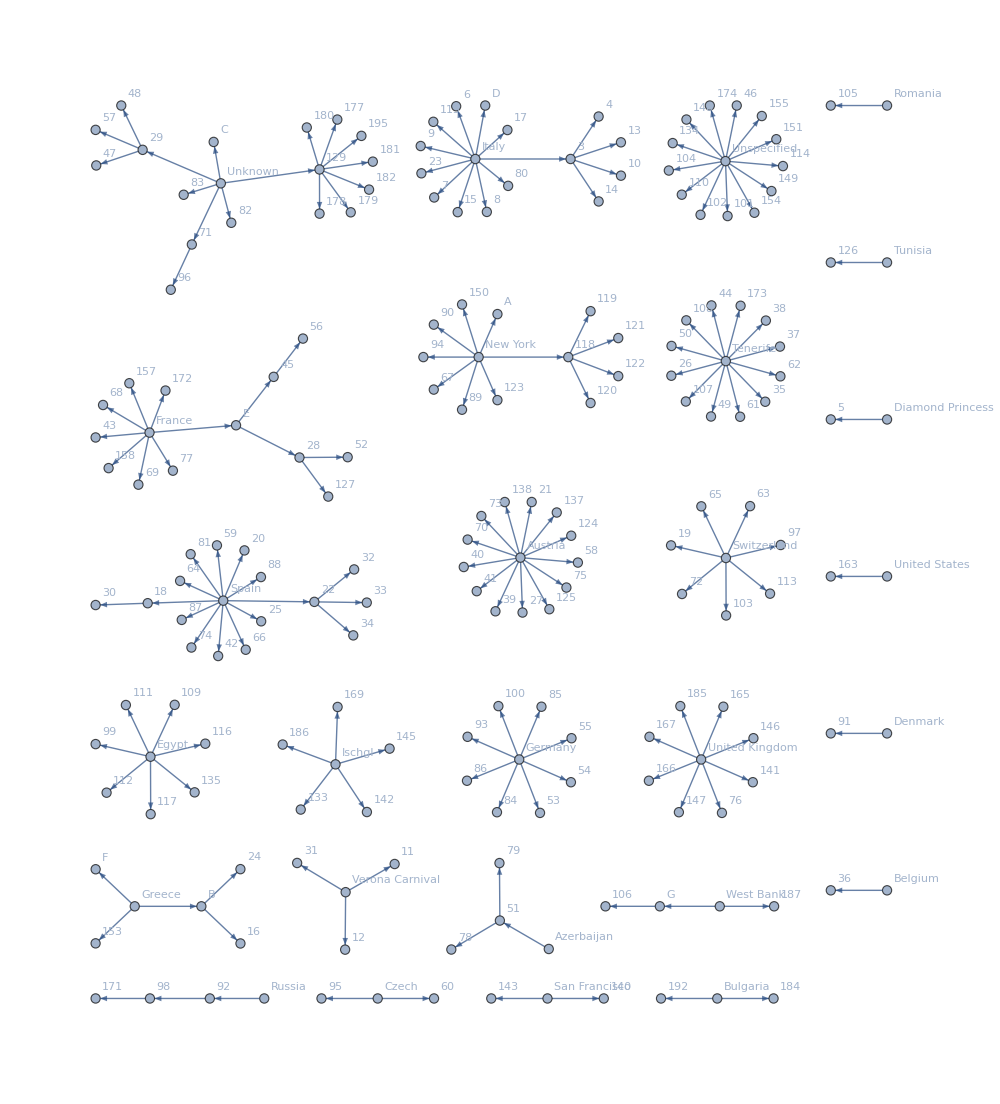

```mathematica
GraphPlot[ContactList,VertexLabels->Automatic,ImageSize->1000,DirectedEdges->True]
```

```mathematica
Export["images/transmissiondiagram.svg",GraphPlot[ContactList,VertexLabels->Automatic,ImageSize->1000,DirectedEdges->True],"SVG"]
```

images/transmissiondiagram.svg

## Making Final Map

```mathematica
ExportImages[key_]:=Module[{filename1,filename2,mystring},
filename1="images/outlinemap"<>If[NumberQ[key],ToString[key],key]<>".svg";
filename2="images/detailedmap"<>If[NumberQ[key],ToString[key],key]<>".jpeg";
Export[filename1,ShowOutlineMap[key],"SVG"];
Export[filename2,ShowDetailedMap[key],"JPEG",ImageResolution->200];
mystring="<h3"<>" id=\""<>If[NumberQ[key],ToString[key],key]<>"\">"<>"Patient Number "<>ToString[key]<>" "<>DataAssociationWithObject[key]["Nickname"]<>" at "<>DataAssociation[ToString[key]]["Location"]<>" <a href=\"#thetop\"  class=\"small button icon fa-level-up\">To Top</a><a href=\""<>"maps/map"<>If[NumberQ[key],ToString[key],key]<>".html"<>"\"  class=\"small button icon fa-map-o\" target=\"_blank\">Interactive Map</a></h3>\n"<>"<div class=\"posts\">\n\t<article>\n\t\t<a href=\""<>filename1<>"\" class=\"image\"><img src=\""<>filename1<>"\" alt=\"\" height=300 /></a>\n\t\t<h4>Outlined Map</h4>\n\t</article>\n\t<article>\n\t\t<a href=\""<>filename2<>"\" class=\"image\"><img src=\""<>filename2<>"\" alt=\"\" height=300/></a>\n\t\t<h4>Detailed Map</h4>\n\t</article>\n</div>\n <h4>Flight History</h4>\n<div>"<>MakeHTMLFlightTable[key]<>"\n</div>\n<h4>Activity History In Israel</h4>\n<div>"<>MakeHTMLTable[key]<>"\n</div>\n<hr class=\"major\" />\n";
mystring
];
ExportImagesWritePageOnly[key_]:=Module[{filename1,filename2,mystring},
filename1="images/outlinemap"<>If[NumberQ[key],ToString[key],key]<>".svg";
filename2="images/detailedmap"<>If[NumberQ[key],ToString[key],key]<>".jpeg";
mystring="<h3"<>" id=\""<>If[NumberQ[key],ToString[key],key]<>"\">"<>"Patient Number "<>ToString[key]<>" "<>DataAssociationWithObject[key]["Nickname"]<>" at "<>DataAssociation[ToString[key]]["Location"]<>" <a href=\"#thetop\"  class=\"small button icon fa-level-up\">To Top</a><a href=\""<>"maps/map"<>If[NumberQ[key],ToString[key],key]<>".html"<>"\"  class=\"small button icon fa-map-o\" target=\"_blank\">Interactive Map</a></h3>\n"<>"<div class=\"posts\">\n\t<article>\n\t\t<a href=\""<>filename1<>"\" class=\"image\"><img src=\""<>filename1<>"\" alt=\"\" height=300 /></a>\n\t\t<h4>Outlined Map</h4>\n\t</article>\n\t<article>\n\t\t<a href=\""<>filename2<>"\" class=\"image\"><img src=\""<>filename2<>"\" alt=\"\" height=300/></a>\n\t\t<h4>Detailed Map</h4>\n\t</article>\n</div>\n <h4>Flight History</h4>\n<div>"<>MakeHTMLFlightTable[key]<>"\n</div>\n<h4>Activity History In Israel</h4>\n<div>"<>MakeHTMLTable[key]<>"\n</div>\n<hr class=\"major\" />\n";
mystring
];
HeadHTML="<!DOCTYPE HTML>
<!--
\tEditorial by HTML5 UP
\thtml5up.net | @ajlkn
\tFree for personal and commercial use under the CCA 3.0 license (html5up.net/license)
-->
<html>
\t<head>
\t\t<title>2019-2020 Israel, West Bank and Gaza Coronavirus Outbreak</title>
\t\t<meta charset=\"utf-8\" />
\t\t<meta name=\"viewport\" content=\"width=device-width, initial-scale=1, user-scalable=no\" />
\t\t<!--[if lte IE 8]><script src=\"assets/js/ie/html5shiv.js\"></script><![endif]-->
\t\t<link rel=\"stylesheet\" href=\"assets/css/main.css\" />
\t\t<!--[if lte IE 9]><link rel=\"stylesheet\" href=\"assets/css/ie9.css\" /><![endif]-->
\t\t<!--[if lte IE 8]><link rel=\"stylesheet\" href=\"assets/css/ie8.css\" /><![endif]-->
\t</head>
\t<body>

\t\t<!-- Wrapper -->
\t\t\t<div id=\"wrapper\">

\t\t\t\t<!-- Main -->
\t\t\t\t\t<div id=\"main\">
\t\t\t\t\t\t<div class=\"inner\">

\t\t\t\t\t\t\t<!-- Header -->
\t\t\t\t\t\t\t\t<header id=\"header\">
\t\t\t\t\t\t\t\t\t<a href=\"index.html\" class=\"logo\"><strong>Editorial</strong> by HTML5 UP</a>
\t\t\t\t\t\t\t\t</header>

\t\t\t\t\t\t\t<!-- Content -->
\t\t\t\t\t\t\t\t<section>
\t\t\t\t\t\t\t\t\t<header class=\"main\">
\t\t\t\t\t\t\t\t\t\t<h1 id=\"thetop\">2019-2020 Israel, West Bank and Gaza Coronavirus Outbreak</h1>
\t\t\t\t\t\t\t\t\t</header>
\t\t\t\t\t\t\t\t\t<span class=\"image main\"><img src=\"images/totalcases.svg\" alt=\"\" /></span>
                                    <div class=\"posts\">
                                        <article>
                                            <a href=\"images/sourcecountries.jpeg\" class=\"image\"><img src=\"images/sourcecountries.jpeg\" alt=\"\" height=300 /></a>
                                            <h4>Source Countries</h4>
                                        </article>
                                        <article>
                                            <a href=\"images/transmissiondiagram.svg\" class=\"image\"><img src=\"images/transmissiondiagram.svg\" alt=\"\" height=300/></a>
                                            <h4>Exposure Diagram Between the Patients</h4>
                                        </article>
                                    </div>
\t\t\t\t\t\t\t\t\t<h3>Introduction</h3>
\t\t\t\t\t\t\t\t\t<p>The patient information and geographic data are based on the press release by the Israeli Ministry of Health from the two following websites: the Hebrew <a href=\"https://t.me/s/MOHreport\">telegraph page</a> and <a href=\"https://www.health.gov.il/Subjects/disease/corona/Pages/press-release.aspx?fbclid=IwAR3dAd_1nauO7hjBk5hjERF1DBnrKT5ac5-OLuyRENQc4iDpQX-KhrERYuE\">the Hebrew page of press releases</a>. Due to the rapid escalation of the pandemic, I have introduced a parser to collect these data automatically, the geographic data are still manually inputed and verified. Expect grammartical mistakes and errors.</p>
                                    <p></p>
\t\t\t\t\t\t\t\t\t<p>This page presents all the cases of coronavirus disease published by the Ministry of Health as of "<>DateString[Now]<>". Please click on the case number for the corresponding cases:</p>\n";
GenerateHREF="<hr class=\"major\" />\n"<>StringJoin@@Table["<a href=\"#"<>If[NumberQ[k],ToString[k],k]<>"\"  class=\"small button icon fa-level-down\">"<>If[NumberQ[k],ToString[k],k]<>"</a>\t",{k,ListOfPatients}]<>"\n<hr class=\"major\" />\n";
GenerateHREFDropdown="<h3>Pick a case to view</h3>\n<select id=\"dropdownmenu\">\n"<>StringJoin@@Table["\t<option value=\"#"<>If[NumberQ[k],ToString[k],k]<>"\">Case Number "<>If[NumberQ[k],ToString[k],k]<>" in Israel "<>DataAssociationWithObject[k]["Nickname"]<>"</option>\n",{k,ListOfPatients}]<>"</select>

                                    <script>
                                        document.getElementById(\"dropdownmenu\").onchange = function() {
                                            if (this.selectedIndex!==0) {
                                                window.location.href = this.value;
                                            }        
                                        };
                                    </script>\n<hr class=\"major\" />\n";
TailHTML="\n\t\t\t\t\t\t</section>
                        <section id=\"banner\">
\t\t\t\t\t\t\t\t\t<div class=\"content\">
\t\t\t\t\t\t\t\t\t\t<h3>Visitors to this map</h3>
\t\t\t\t\t\t\t\t\t\t<p>This map is created by Zhuohui Zhang <a href=\"mailto:zhuohui.zhang@gmail.com\">zhuohui.zhang@gmail.com</a> based on the information released by the Israeli Ministry of Health</p>
\t\t\t\t\t\t\t\t\t\t<ul class=\"actions\">
\t\t\t\t\t\t\t\t\t\t\t<li><a href=\"https://t.me/s/MOHreport\" class=\"button big\">Learn More</a></li>
\t\t\t\t\t\t\t\t\t\t</ul>
\t\t\t\t\t\t\t\t\t</div>
\t\t\t\t\t\t\t\t\t<span class=\"image object\">
\t\t\t\t\t\t\t\t\t\t<a href=\"https://m.maploco.com/details/7105yzdd\"><img style=\"border:0px;\" src=\"https://www.maploco.com/vmap/s/10030225.png\" alt=\"Locations of Site Visitors\" title=\"Locations of Site Visitors\"/></a>
\t\t\t\t\t\t\t\t\t</span>
                            <hr class=\"major\" />
\t\t\t\t        </section>
\t\t\t\t\t\t</div>
\t\t\t\t\t</div>

\
\t\t<!-- Scripts -->
\t\t\t<script src=\"assets/js/jquery.min.js\"></script>
\t\t\t<script src=\"assets/js/skel.min.js\"></script>
\t\t\t<script src=\"assets/js/util.js\"></script>
\t\t\t<!--[if lte IE 8]><script src=\"assets/js/ie/respond.min.js\"></script><![endif]-->
\t\t\t<script src=\"assets/js/main.js\"></script>

\t</body>
</html>";
```

## Execute

```mathematica
Export["images/frontpage.jpeg",GeoListPlot[{Entity["Country","China"],Entity["Country","SouthKorea"],Entity["Country","Italy"],Entity["Country","France"],Entity["Country","Switzerland"],Entity["Country","Spain"],Entity["Country","Andorra"],Entity["Country","SanMarino"],Entity["Country","Austria"],Entity["Country","Japan"],Entity["Country","Singapore"],Entity["Country","Thailand"],Entity["Country","Germany"]},ImageSize->500],"JPEG"];
```

```mathematica
Table[ExportImages[key],{key,Range[110,155]}];
```

GeoPosition::invpos: GeoPosition[{Actions[StartLocation][Coordinate],Actions[EndLocation][Coordinate]}] is not a valid position specification.

GeoMarker::invpts: If[Missing[KeyAbsent,128][Address]==Entity,Missing[KeyAbsent,128][Address][Object]] is not a valid GeoMarker coordinates specification.

GeoPosition::invpos: GeoPosition[{Actions[StartLocation][Coordinate],Actions[EndLocation][Coordinate]}] is not a valid position specification.

GeoMarker::invpts: If[Missing[KeyAbsent,128][Address]==Entity,Missing[KeyAbsent,128][Address][Object]] is not a valid GeoMarker coordinates specification.

Table::iterb: Iterator {act,Missing[KeyAbsent,128][]} does not have appropriate bounds.

Table::nliter: Non-list iterator converttotd$136014[{act,Missing[KeyAbsent,128][]}] at position 2 does not evaluate to a real numeric value.

Table::iterb: Iterator {act,Missing[KeyAbsent,128][]} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

Table::nliter: Non-list iterator converttotd$136029[{act,Missing[KeyAbsent,128][]}] at position 2 does not evaluate to a real numeric value.

StringJoin::string: String expected at position 2 in <h3 id="128">Patient Number Missing[KeyAbsent, 128][Key] <>«1»<> at Missing[KeyAbsent, 128][Address][Object][Name] <a href="#thetop"  class="small button icon fa-level-up">To Top</a><a href="maps/map128.html"  class="small button icon fa-map-o" target="_blank">Interactive Map</a></h3>
<div class="posts">
	<article>
		<a href="images/outlinema…<th>At Address</th>
		<th>In</th>
		<th></th>
		<th>From Around</th>
		<th>At Address</th>
		<th>In</th>
	</tr>
	<tr>
		<td></td>
		<td><img src="redarrow.png" alt="Redarrow" height="30" width="40"/></td>
		<td></td>
	</tr>
	<tr>
	</tr>
</table></div>
</div>
<hr class="major" />
.

GeoPosition::invpos: GeoPosition[{Actions[StartLocation][Coordinate],Actions[EndLocation][Coordinate]}] is not a valid position specification.

General::stop: Further output of GeoPosition::invpos will be suppressed during this calculation.

GeoMarker::invpts: If[Missing[KeyAbsent,129][Address]==Entity,Missing[KeyAbsent,129][Address][Object]] is not a valid GeoMarker coordinates specification.

General::stop: Further output of GeoMarker::invpts will be suppressed during this calculation.

Table::nliter: Non-list iterator converttotd$136227[{act,Missing[KeyAbsent,129][]}] at position 2 does not evaluate to a real numeric value.

General::stop: Further output of Table::nliter will be suppressed during this calculation.

StringJoin::string: String expected at position 2 in <h3 id="129">Patient Number Missing[KeyAbsent, 129][Key] <>«1»<> at Missing[KeyAbsent, 129][Address][Object][Name] <a href="#thetop"  class="small button icon fa-level-up">To Top</a><a href="maps/map129.html"  class="small button icon fa-map-o" target="_blank">Interactive Map</a></h3>
<div class="posts">
	<article>
		<a href="images/outlinema…<th>At Address</th>
		<th>In</th>
		<th></th>
		<th>From Around</th>
		<th>At Address</th>
		<th>In</th>
	</tr>
	<tr>
		<td></td>
		<td><img src="redarrow.png" alt="Redarrow" height="30" width="40"/></td>
		<td></td>
	</tr>
	<tr>
	</tr>
</table></div>
</div>
<hr class="major" />
.

StringJoin::string: String expected at position 2 in <h3 id="130">Patient Number Missing[KeyAbsent, 130][Key] <>«1»<> at Missing[KeyAbsent, 130][Address][Object][Name] <a href="#thetop"  class="small button icon fa-level-up">To Top</a><a href="maps/map130.html"  class="small button icon fa-map-o" target="_blank">Interactive Map</a></h3>
<div class="posts">
	<article>
		<a href="images/outlinema…<th>At Address</th>
		<th>In</th>
		<th></th>
		<th>From Around</th>
		<th>At Address</th>
		<th>In</th>
	</tr>
	<tr>
		<td></td>
		<td><img src="redarrow.png" alt="Redarrow" height="30" width="40"/></td>
		<td></td>
	</tr>
	<tr>
	</tr>
</table></div>
</div>
<hr class="major" />
.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

```mathematica
Monitor[Export["index.html",HeadHTML<>GenerateHREFDropdown<>StringJoin@@Table[ExportImagesWritePageOnly[key],{key,Reverse[ListOfPatients]}]<>TailHTML,"Text"],key]
```

index.html

```mathematica
Monitor[Table[ExportImages[key],{key,Reverse[ListOfPatients]}],key]
```

```mathematica
Export["images/detailedmap127.jpeg",ShowDetailedMap[127],"JPEG",ImageResolution-> 200]
```

images/detailedmap127.jpeg